Plotting the Hexagonal lattice

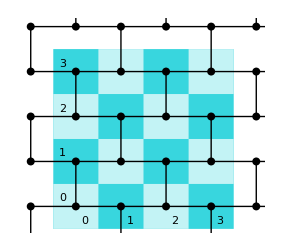

```mathematica
(* by unit cell? *)
unitCellXY[xx_, yy_ ]  := {Point[{xx,yy}], Point[{xx,yy+1}], Line[{ {xx,yy}, {xx,yy+1} }], Line[{ {xx,yy}, {xx+1,yy} }], Line[{ {xx,yy+1}, {xx+1,yy+1} }]};
cellpositions = {
Table[ {x,y}, {x,0,4,2}, {y,0,4,2}]
,Table[ {x,y}, {x,-1,3,2}, {y,-1,3,2}]
};
xcoordaxis = Table[ Text[ j , {j+.2,-.3}],{j,0,3}];
ycoordaxis = Table[ Text[ j , {-.3,j+.2}],{j,0,3}];
softgrid = Table[ If[EvenQ[ x+ y], Rectangle[ {x-.5,y-.5}, {x+.5,y+.5} ], {} ], {x,0,3},{y,0,3} ];

SetOptions[Graphics,BaseStyle->FontSize->20];
bgcol1 = RGBColor[0.22,0.84,0.87];
bgcol2 = Lighter[bgcol1, .7 ] ;

hexgrid = Graphics[ {
bgcol1, Rectangle[ {-.5,-.5},{3.5,3.5}]
, bgcol2, softgrid
, Black, PointSize[.02]
,Table[ unitCellXY[ pos[[1]], pos[[2]] ], {pos, Flatten[ cellpositions, 2 ] } ]
, xcoordaxis, ycoordaxis, 

}
, PlotRange->{{ -1.1,4.1}, {-0.5,4.1} }

]
```

```mathematica
Export[ "hexgrid.pdf", hexgrid ]
```

hexgrid.pdf

#### Old approach (can be removed)

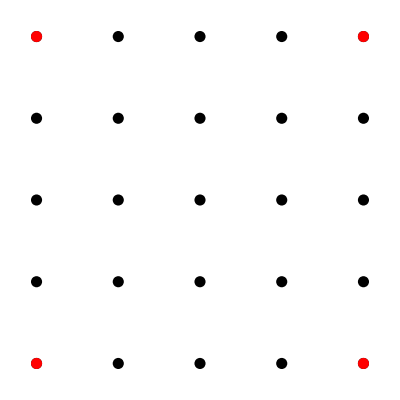

```mathematica
(* Define points *)
xrange = Range[0, 4]; yrange = Range[0,4];
coords = Table[ { j , k }, {j,xrange}, {k,yrange} ];
allpoints = Map[ Point, coords , {2}] ;
specialcoords = {{0,0}, {4,4}, {0,4}, {4,0}};
specialpoints = Map[ Point, specialcoords ] ;

(* Define lines *)

Graphics[ {
PointSize[.02] , allpoints
, Red, specialpoints 


}]
```

#### Scratchpad